### Optimal Response to a Passive Eager Strategy

```mathematica
ClearAll["Global`*"]
```

b(t) = (-1+ⅇ^(-3 t))/(-1+1/ⅇ^3)

b(0.5) = 0.817574

Solution: {{a[t]→10.6667 ⅇ^(-3. t) (0.953734-0.953734 ⅇ^(3. t)+1. ⅇ^(3. t) t)}}

a(t) = 10.6667 ⅇ^(-3. t) (0.953734-0.953734 ⅇ^(3. t)+1. ⅇ^(3. t) t)

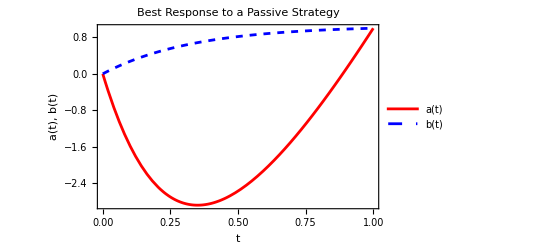

a(t) = 26 t-25 t^2

Solution: {{a[t]→26 t-25 t^2}}

b(0.5) = 0.5

b(t) = t

```mathematica
(*Define constants*)λ=20;κ=0.1;σ=3;

(*Define b(t)*)
b[t_] := (Exp[-σ t] - 1) / (Exp[-σ] - 1); (* eager *)

(*Print b(t) to check its definition*)
Print["b(t) = ",b[t]];
Print["b(0.5) = ",b[0.5]];

(*Define the differential equation for a(t)*)
solveForA[]:=Module[{eqns,bcs,sol,aSol},eqns={a''[t]==-(λ/2) (b''[t]+ κ b'[t])};(*b''[t]=0 for b(t)=t*)
bcs={a[0]==0,a[1]==1};
sol=DSolve[{eqns,bcs},a[t],t];
Print["Solution: ",sol];
aSol=a[t]/. sol[[1]];
aSol];

(*Print a(t) to check its definition*)
aSolution=solveForA[];
Print["a(t) = ",aSolution];

(*Plot both a(t) and b(t) with b(t) as a dashed line*)
Plot[{aSolution,b[t]},{t,0,1},PlotLegends->{"a(t)","b(t)"},PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{{"a(t), b(t)","\!\(\*SubscriptBox[\(ξ\), \(a\)]\) = "<>ToString[ξa]<>", σ="<>ToString[σ]},{"t","κ="<>ToString[κ]<>", λ="<>ToString[λ]}},PlotLabel->"Best Response to a Passive Strategy",PlotRange->All]
```

### Calculate Total Cost

```mathematica
ClearAll["Global`*"]
λ=10;κ=10;
a[t_]=26 t-25 t^2;
b[t_]=t;
aPrime[t_]=D[a[t],t];
bPrime[t_]=D[b[t],t];

(*Define the functionals*)
functional1=(aPrime[t]+λ bPrime[t]) aPrime[t];
functional2=κ (a[t]+λ b[t]) aPrime[t];

(*Calculate the integrals*)
integral1=Integrate[functional1,{t,0,1}];
integral2=Integrate[functional2,{t,0,1}];
total_cost=integral1+integral2
```

-427/3